```mathematica
SetOptions[
Plot,
BaseStyle->FontSize->14,
ImageSize->{Automatic,300},
PlotRange->All,
Frame->True,
PlotRangePadding->{Scaled[0.008],Scaled[0.02]},
FrameStyle->Thickness[0.001],
AspectRatio->1
];
```

```mathematica
energyColors=Lighter/@{Red,Blue,Green}
```

{RGBColor[1, Rational[1, 3], Rational[1, 3]],RGBColor[Rational[1, 3], Rational[1, 3], 1],RGBColor[Rational[1, 3], 1, Rational[1, 3]]}

```mathematica
splittingColors=MapThread[Blend[{#1,#2},0.5]&,{energyColors,RotateRight[energyColors,2]}]
```

{RGBColor[0.6666666666666666, 0.3333333333333333, 0.6666666666666667],RGBColor[0.3333333333333333, 0.6666666666666667, 0.6666666666666666],RGBColor[0.6666666666666667, 0.6666666666666666, 0.3333333333333333]}

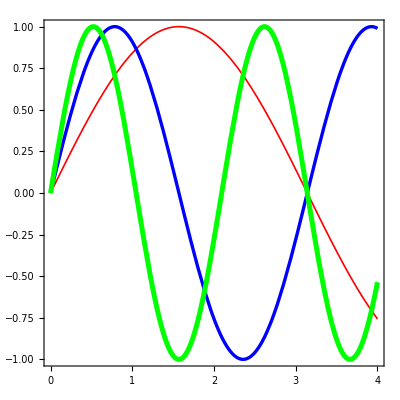

```mathematica
Plot[
Evaluate[Table[Sin[n x],{n,1,3}]],
{x,0,4},
PlotStyle->{{Red,Thickness[0.003]},{Blue,Thickness[0.006]},{Green,Thickness[0.009]}}
]
```

```mathematica
Evals[Ω_,Δ_,q_]:={1/2 Root[-8 q Δ^2+(-4 Δ^2-4 Ω^2) #1+2 q #1^2+#1^3&,1],1/2 Root[-8 q Δ^2+(-4 Δ^2-4 Ω^2) #1+2 q #1^2+#1^3&,2],1/2 Root[-8 q Δ^2+(-4 Δ^2-4 Ω^2) #1+2 q #1^2+#1^3&,3]};
```

```mathematica
qRmagic=0.348;
δrange=4;
```

```mathematica
qRList=Insert[
Table[qR,{qR,0.01,1.01,0.1}],
qRmagic,5
]
```

{0.01,0.11,0.21,0.31,0.348,0.41,0.51,0.61,0.71,0.81,0.91,1.01}

```mathematica
dw=0.003;
```

```mathematica
darkness[qR_]:=qR/qRmagic/;qR≤qRmagic;
darkness[qR_]:=1-(qR-qRmagic)/(1-qRmagic)/;qR>qRmagic;
```

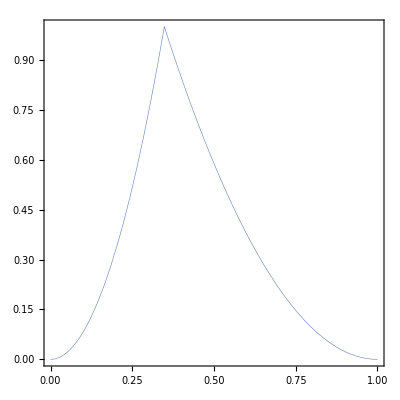

```mathematica
Plot[darkness[qR]^2,{qR,0,1},PlotStyle->Thickness[0.001]]
```

```mathematica
barePlot=Plot[
{δ,-δ},
{δ,-δrange/2,δrange/2},
PlotStyle->{{Gray,Dashed,Thickness[dw],Opacity[0.5]}}
];
```

```mathematica
makeEnergyPlot[qR_]:=Module[{p1,p2},
p1=Plot[
-qR,
{δ,-δrange/2,δrange/2},
PlotStyle->{{Gray,Dashed,Thickness[dw],Opacity[darkness[qR]^2]}}
];

p2=Plot[
Evals[2π,2π*δ,2π*qR]/(2π)//Evaluate,
{δ,-δrange/2,δrange/2},
PlotStyle->({#,Thickness[If[qR==qRmagic,2*dw,dw]],Opacity[darkness[qR]^1]}&/@energyColors)
];

Show[p1,p2,FrameLabel->{"Δ/Ω","(ω_n-q)/Ω"},PlotRange->{{-δrange/2,δrange/2},{-δrange/2,δrange/2}}]
];
```

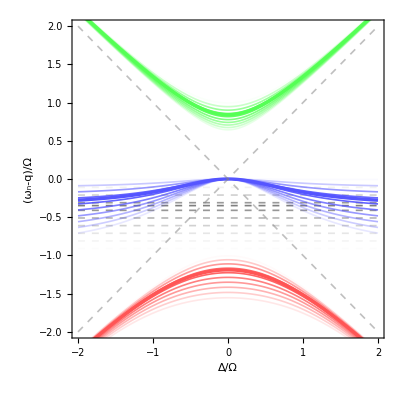

```mathematica
pA=Show[Append[Map[makeEnergyPlot,qRList],barePlot]]
```

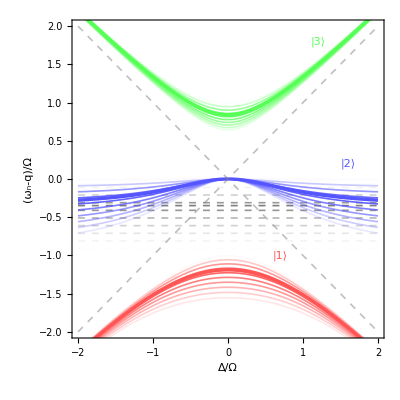

```mathematica
pA=Show[pA,Epilog->{
Text[Style["|3⟩",energyColors[[3]]],{1.2,1.8}],
Text[Style["|2⟩",energyColors[[2]]],{1.6,0.2}],
Text[Style["|1⟩",energyColors[[1]]],{0.7,-1}]
}
]
```

```mathematica
splittingPlot[qR_]:=(
Elist=Evals[2π,2π*δ,2π*qR];
Plot[
Evaluate[(2π)^-1{Elist[[2]]-Elist[[1]],Elist[[3]]-Elist[[2]],Elist[[3]]-Elist[[1]]}],
{δ,0,δrange/2},
FrameLabel->{"Δ/Ω","ω_ij/Ω"},
PlotRange->{{0,δrange/2},{0,2δrange/2}},
PlotStyle->({#,Thickness[If[qR==qRmagic,3*dw,1.5*dw]],Opacity[darkness[qR]^1]}&/@splittingColors),
FrameTicks->{{Automatic,Automatic},{{0,1,2},Automatic}}
]
);
```

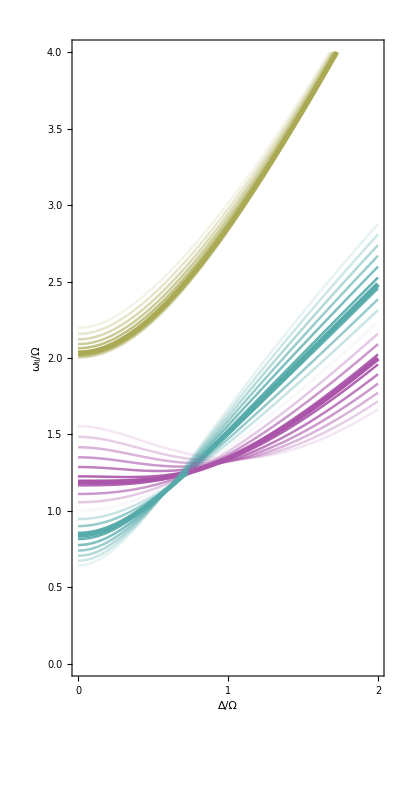

```mathematica
pB=Show[
Map[
splittingPlot,
qRList
],
AspectRatio->2,
PlotRangePadding->{Scaled[0.01],Scaled[0.02]}
]
```

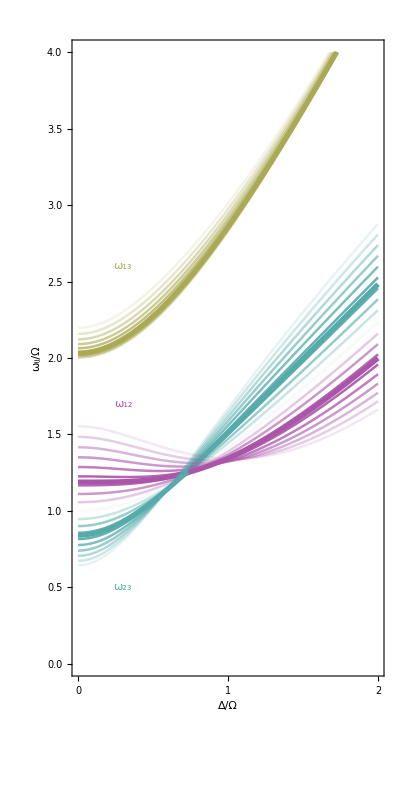

```mathematica
pB=Show[
pB,
Epilog->{
Text[Style["ω_13",splittingColors[[3]]],{0.3,2.6}],
Text[Style["ω_12",splittingColors[[1]]],{0.3,1.7}],
Text[Style["ω_23",splittingColors[[2]]],{0.3,0.5}]
}
]
```

```mathematica
out=With[{size=300},
Row[
Map[
Show[#,ImageSize->{Automatic,size},
ImagePadding->{{40,10},{50,10}}
]&,
{pA,pB}
]
]
]
```

-Graphics--Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Michael\Dropbox\Dressed_paper\figures

```mathematica
MapThread[
Export[#2,#1,ImageResolution->300]&,
{
{out,pA,pB},{"figure_1.pdf","figure_1a.pdf","figure_1b.pdf"}
}
]
```

{figure_1.pdf,figure_1a.pdf,figure_1b.pdf}